# Math 223: Homework 6

<Zihan Xu>

<3/15/2023>

## Problem 1

The Fresnel sine integral is given by S(x)=∫_0^x sin((π t^2)/2)ⅆt. The command to evaluate S(x) in Mathematica is FresnelS[x].

#### (a) Use integration-by-parts to find the leading behavior of S(x) as x->0^+ and compare your result with what Mathematica computes, which might be slightly different from what you compute. Comment on what you find and which approximation you believe yields a better approximation overall.

Solution:

We apply integration by parts using u= sin((π t^2)/2) and ⅆv = ⅆt, so that ⅆu = cos((π t^2)/2)π t ⅆt and v = t, and find

S(x)= x sin((π x^2)/2)- ∫_0^x cos[(π t^2)/2] π t^2 ⅆt

Repeated integration-by-parts again, we find
 S(x)= x sin((π x^2)/2)- ∫_0^x cos[(π t^2)/2] π t^2 ⅆt
        = x sin((π x^2)/2) - (π x^3)/3 cos[(π x^2)/2] -∫_0^x sin[(π t^2)/2] π^2 t^4 ⅆt
        = x sin((π x^2)/2) - (π x^3)/3 cos[(π x^2)/2] + O(x^5)

Thus, we have the leading behavior S(x)∼ x sin((π x^2)/2) - (π x^3)/3 cos[(π x^2)/2] as x->0^+

```mathematica
Problem1Behavior = Collect[Series[FresnelS[x],{x,0,3},Assumptions->x>0],x]
```

(π x^3)/6

```mathematica
Problem1Exact[x_]=Refine[FresnelS[x],Assumptions->x>0]
```

FresnelS[x]

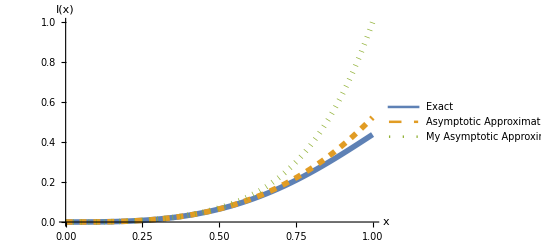

```mathematica
Plot[{Problem1Exact[x],Problem1Behavior,x Sin[(π x^2)/2]-(π x^3)/3 Cos[(π x^2)/2]},{x,0,1},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]],Directive[Dotted,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact", "Asymptotic Approximation","My Asymptotic Approximation"}]
```

From the figure, we can observe that the asymptotic approximation Mathematica computed (orange dashed line) has better performance than my approximation using integration-by-parts (green dotted line). If I include more terms, the performance would be better.

#### (b) Use ∫_0^∞ sin((π t^2)/2)ⅆt=1/2, and integration-by-parts to find the leading behavior of S(x) as x->+∞ (Hint: Consider a substitution prior to performing integration-by-parts). Compare your result with what Mathematica computes and discuss what you find.

Solution:

S(x)=∫_0^∞ sin((π t^2)/2)ⅆt -∫_x^∞ sin((π t^2)/2)ⅆt = 1/2-∫_x^∞ sin((π t^2)/2)ⅆt

Consider a substitution u=(π t^2)/2 and obtain ∫_x^∞ sin((π t^2)/2)ⅆt = 1/(√(2π))∫_((π x^2)/2)^∞ (sin(u))/(√u)ⅆu.
To obtain the asymptotic expansion of ∫_((π x^2)/2)^∞ (sin(u))/(√u)ⅆu, we can perform integration by parts:
∫_((π x^2)/2)^∞ (sin(u))/(√u)ⅆu = (- cos(u))/(√u)|_((π x^2)/2)^∞-1/2∫_((π x^2)/2)^∞ (cos(u))/u^(3/2)ⅆu                         （integration by parts for ∫_((π x^2)/2)^∞ (sin(u))/(√u)ⅆu : u=1/(√u), ⅆv = sin(u)ⅆu, so ⅆu = -1/(2 u^(3/2)), v = -cos(u)）
                          =(cos((π x^2)/2))/(√((π x^2)/2)) -1/2((sin(u))/u^(3/2)|_((π x^2)/2)^∞+ 3/2∫_((π x^2)/2)^∞ (sin(u))/u^(5/2)ⅆu)  （integration by parts for ∫_((π x^2)/2)^∞ (cos(u))/u^(3/2)ⅆu : u=1/u^(3/2), ⅆv = cos(u)ⅆu, so ⅆu = -3/(2 u^(5/2)), v = sin(u)）
                          =(cos((π x^2)/2))/(√((π x^2)/2))+(sin((π x^2)/2))/(2((π x^2)/2)^(3/2))- 3/4∫_((π x^2)/2)^∞ (sin(u))/u^(5/2)ⅆu

We can plug it into S(x):
S(x)= 1/2-∫_x^∞ sin((π t^2)/2)ⅆt
       =  1/2-1/(√(2π))∫_((π x^2)/2)^∞ (sin(u))/(√u)ⅆu
       =  1/2-1/(√(2π))((cos((π x^2)/2))/(√((π x^2)/2))+(sin((π x^2)/2))/(2((π x^2)/2)^(3/2))-3/4∫_((π x^2)/2)^∞ (sin(u))/u^(5/2)ⅆu)
       = 1/2-(cos((π x^2)/2))/(π x)-(sin((π x^2)/2))/(π^2 x^3)+O(x^-5)
Therefore, we can obtain the leading behavior: S(x) ∼ 1/2 -(cos((π x^2)/2))/(π x)-(sin((π x^2)/2))/(π^2 x^3)  as  x-> ∞

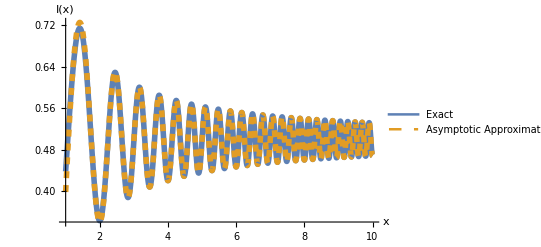

```mathematica
Plot[{Problem1Exact[x], 1/2 -Cos[(π x^2)/2]/(π x)-Sin[(π x^2)/2]/(π^2 x^3)},{x,1,10},PlotRange->All, PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact", "Asymptotic Approximation"}]
```

## Problem 2

#### Show that

#### ∫_0^1 (ⅇ^x-ⅇ^(x t))/(1-t)ⅆt ∼ ⅇ^x log(x)+ⅇ^xγ+..., x->+∞,

#### where γ is the Euler-Mascheroni constant, defined according to

#### γ=∫_0^∞ (1/(u+1)-ⅇ^-u)ⅆu/u.

#### (Hint: make a substitution that yields x as a limit of integration, and consider the trick we used in Lecture 11 to manufacture the definition of γ given above.)

Solution:

Consider substitution s=xt and ⅆs = x ⅆt and we can obtain
I(x) = ∫_0^1 (ⅇ^x-ⅇ^(x t))/(1-t)ⅆt 
       = ⅇ^x∫_0^1 1/(1-t)ⅆt -∫_0^1 ⅇ^(x t)/(1-t)ⅆt
        = ⅇ^x∫_0^1 1/(1-t)ⅆt -∫_0^x ⅇ^s/(x-s)ⅆs
        = ⅇ^x∫_0^1 1/(1-t)ⅆt -ⅇ^x∫_0^x ⅇ^(s-x)/(x-s)ⅆs (let u=x-s, ⅆu = -ⅆs)
        = ⅇ^x(∫_0^1 1/(1-t)ⅆt -∫_0^x ⅇ^-u/u ⅆu)
Note that ∫_0^1 1/(1-t)ⅆt = ∫_0^x 1/u ⅆu if we make the same substitution u=x(1-t). Thus, we can get
I(x) =  ⅇ^x(∫_0^x 1/u ⅆu -∫_0^x ⅇ^-u/u ⅆu)
       =  ⅇ^x(∫_0^x 1/u ⅆu -∫_0^x ⅇ^-u/u(1-ⅇ^u/(u+1)+ⅇ^u/(u+1))ⅆu)
       =  ⅇ^x(∫_0^x 1/u ⅆu -∫_0^x ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu -∫_0^x 1/(u(u+1))ⅆu)
       =  ⅇ^x(∫_0^x 1/u(1-1/(u+1))ⅆu -∫_0^x ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu )
       =  ⅇ^x(∫_0^x 1/(u+1)ⅆu -∫_0^x ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu )

The Taylor expansion for the first integral ∫_0^x 1/(u+1)ⅆu:

```mathematica
Series[Integrate[1/(u+1),{u,0,x}],{x,∞,2}]
```

Log[x]+1/x-1/(2 x^2)+O[1/x]^3

Consider the second integral ∫_0^x ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu= ∫_0^∞ ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu - ∫_x^∞ ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu

We have  ∫_0^∞ ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu = -γ or equivalently γ =∫_0^∞ ⅇ^-u/u(ⅇ^u/(u+1)-1)ⅆu=∫_0^∞ (1/(u+1)-ⅇ^-u)ⅆu/u:

```mathematica
Integrate[ⅇ^-u/u(1-ⅇ^u/(u+1)),{u,0,∞}]
```

-EulerGamma

The Taylor expansion for ∫_x^∞ ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu:

```mathematica
Series[Integrate[ⅇ^-u/u(1-ⅇ^u/(u+1)),{u,x,∞}],{x,∞,2}]
```

ConditionalExpression[(-1/x+1/(2 x^2)+O[1/x]^3)+ⅇ^(-x+O[1/x]^3) (1/x-(1/x)^2+O[1/x]^3), O[1/x]^3==0]

Combine them together, we will get the following asymptotic behavior:

∫_0^1 (ⅇ^x-ⅇ^(x t))/(1-t)ⅆt  =  ⅇ^x(∫_0^x 1/(u+1)ⅆu -∫_0^x ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu )
                       =   ⅇ^x(∫_0^x 1/(u+1)ⅆu -∫_0^∞ ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu + ∫_x^∞ ⅇ^-u/u(1-ⅇ^u/(u+1))ⅆu )
                       =  ⅇ^x(Log[x]+1/x-1/(2 x^2)+O[1/x]^3-(-γ) +(-1/x+1/(2 x^2)+O[1/x]^3)+ⅇ^(-x+O[1/x]^3) (1/x-(1/x)^2+O[1/x]^3))
                      =  ⅇ^x Log[x] + ⅇ^xγ + ⅇ^(O[1/x]^3)(1/x-(1/x)^2+O[1/x]^3)
Therefore, ∫_0^1 (ⅇ^x-ⅇ^(x t))/(1-t)ⅆt ∼  ⅇ^x Log[x] + ⅇ^xγ + ... as x->+∞ where γ =∫_0^∞ (1/(u+1)-ⅇ^-u)ⅆu/u

```mathematica
Problem2Exact[x_]=Refine[Integrate[(ⅇ^x-ⅇ^(x t))/(1-t),{t,0,1}],Assumptions->x>0]
```

ⅇ^x (EulerGamma-CoshIntegral[x]+Log[x]+SinhIntegral[x])

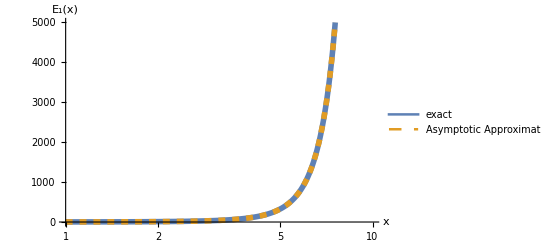

```mathematica
LogLinearPlot[{Problem2Exact[x],Exp[x](EulerGamma+Log[x])},{x,1,10},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["E_1(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact","Asymptotic Approximation"}]
```